# IV Nonlinear optomechanics

Lecamwasam, R, Iakovleva, T, & Twamley, J (2024). Quantum metrology with linear Lie algebra parameterizations Phys. Rev. Res., 6, 043137 arxiv:2311.12446.

See section IV of the main text, and section IV of the supplementary material.

Run OperatorAlgebrav2.nb before running this notebook.

## Preliminaries

### Algebra

```mathematica
Commutator[p̂,x̂,-ⅈ ℏ ];
Commutator[x̂,n̂,0];
Commutator[p̂,n̂,0];

algebra={1,n̂,n̂∘n̂,x̂,p̂,x̂∘x̂,p̂∘p̂,x̂∘p̂,n̂∘x̂,n̂∘p̂}
AlgCommTable[algebra,Xj->False]
```

{1,n̂,n̂∘n̂,x̂,p̂,x̂∘x̂,p̂∘p̂,x̂∘p̂,n̂∘x̂,n̂∘p̂}

| 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n̂ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n̂∘n̂ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x̂ | 0 | 0 | 0 | 0 | ⅈ ℏ | 0 | 2 ⅈ ℏ p̂ | ⅈ ℏ x̂ | 0 | ⅈ ℏ n̂
p̂ | 0 | 0 | 0 | -ⅈ ℏ | 0 | -2 ⅈ ℏ x̂ | 0 | -ⅈ ℏ p̂ | -ⅈ ℏ n̂ | 0
x̂∘x̂ | 0 | 0 | 0 | 0 | 2 ⅈ ℏ x̂ | 0 | 2 ℏ (ℏ+2 ⅈ x̂∘p̂) | 2 ⅈ ℏ x̂∘x̂ | 0 | 2 ⅈ ℏ n̂∘x̂
p̂∘p̂ | 0 | 0 | 0 | -2 ⅈ ℏ p̂ | 0 | -2 ℏ (ℏ+2 ⅈ x̂∘p̂) | 0 | -2 ⅈ ℏ p̂∘p̂ | -2 ⅈ ℏ n̂∘p̂ | 0
x̂∘p̂ | 0 | 0 | 0 | -ⅈ ℏ x̂ | ⅈ ℏ p̂ | -2 ⅈ ℏ x̂∘x̂ | 2 ⅈ ℏ p̂∘p̂ | 0 | -ⅈ ℏ n̂∘x̂ | ⅈ ℏ n̂∘p̂
n̂∘x̂ | 0 | 0 | 0 | 0 | ⅈ ℏ n̂ | 0 | 2 ⅈ ℏ n̂∘p̂ | ⅈ ℏ n̂∘x̂ | 0 | ⅈ ℏ n̂∘n̂
n̂∘p̂ | 0 | 0 | 0 | -ⅈ ℏ n̂ | 0 | -2 ⅈ ℏ n̂∘x̂ | 0 | -ⅈ ℏ n̂∘p̂ | -ⅈ ℏ n̂∘n̂ | 0

```mathematica
MatrixForm/@AdjointRep[algebra]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ℏ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 2 ℏ^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | -2 ℏ^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | -4 ⅈ ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ℏ),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ℏ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ℏ | 0 | 0)}

### Ideal

```mathematica
ideal={1,n̂,x̂,p̂};
AlgCommTable[algebra,ideal]
```

| 1 | n̂ | x̂ | p̂
1 | 0 | 0 | 0 | 0
n̂ | 0 | 0 | 0 | 0
n̂∘n̂ | 0 | 0 | 0 | 0
x̂ | 0 | 0 | 0 | ⅈ ℏ
p̂ | 0 | 0 | -ⅈ ℏ | 0
x̂∘x̂ | 0 | 0 | 0 | 2 ⅈ ℏ x̂
p̂∘p̂ | 0 | 0 | -2 ⅈ ℏ p̂ | 0
x̂∘p̂ | 0 | 0 | -ⅈ ℏ x̂ | ⅈ ℏ p̂
n̂∘x̂ | 0 | 0 | 0 | ⅈ ℏ n̂
n̂∘p̂ | 0 | 0 | -ⅈ ℏ n̂ | 0

```mathematica
algebra
MatrixForm/@AdjointRep[algebra,ideal]
```

{1,n̂,n̂∘n̂,x̂,p̂,x̂∘x̂,p̂∘p̂,x̂∘p̂,n̂∘x̂,n̂∘p̂}

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ ℏ
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | -ⅈ ℏ | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ ℏ
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -2 ⅈ ℏ | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -ⅈ ℏ | 0
0 | 0 | 0 | ⅈ ℏ),(0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ ℏ
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | -ⅈ ℏ | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

### Structure

```mathematica
AlgStructureΓFull[algebra]
```

{ | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(1,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(1,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(n̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(n̂∘n̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘n̂,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(x̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,p̂) | ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0 | 0 | 0
Γ_(x̂,x̂∘p̂) | 0 | 0 | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂,n̂∘p̂) | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(p̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,x̂) | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,x̂∘x̂) | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,x̂∘p̂) | 0 | 0 | 0 | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0
Γ_(p̂,n̂∘x̂) | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(x̂∘x̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,p̂) | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,p̂∘p̂) | 2 ℏ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ ℏ | 0 | 0
Γ_(x̂∘x̂,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘x̂,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(p̂∘p̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂∘p̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂∘p̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂∘p̂,x̂) | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0 | 0 | 0
Γ_(p̂∘p̂,p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂∘p̂,x̂∘x̂) | -2 ℏ^2 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ ℏ | 0 | 0
Γ_(p̂∘p̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(p̂∘p̂,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0
Γ_(p̂∘p̂,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ
Γ_(p̂∘p̂,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(x̂∘p̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘p̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘p̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘p̂,x̂) | 0 | 0 | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘p̂,p̂) | 0 | 0 | 0 | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘p̂,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0 | 0 | 0 | 0
Γ_(x̂∘p̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ | 0 | 0 | 0
Γ_(x̂∘p̂,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(x̂∘p̂,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ℏ | 0
Γ_(x̂∘p̂,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ℏ, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(n̂∘x̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘x̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘x̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘x̂,x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘x̂,p̂) | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘x̂,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘x̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ ℏ
Γ_(n̂∘x̂,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ℏ | 0
Γ_(n̂∘x̂,n̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘x̂,n̂∘p̂) | 0 | 0 | ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0, | 1 | n̂ | n̂∘n̂ | x̂ | p̂ | x̂∘x̂ | p̂∘p̂ | x̂∘p̂ | n̂∘x̂ | n̂∘p̂
Γ_(n̂∘p̂,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘p̂,n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘p̂,n̂∘n̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘p̂,x̂) | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘p̂,p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘p̂,x̂∘x̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ ℏ | 0
Γ_(n̂∘p̂,p̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘p̂,x̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ℏ
Γ_(n̂∘p̂,n̂∘x̂) | 0 | 0 | -ⅈ ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
Γ_(n̂∘p̂,n̂∘p̂) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0}

## Dynamics

### Constant Hamiltonian

```mathematica
$Assumptions={ℏ>0,ω>0,m>0,Ω>0,G0>0,ϵ>0,ωG>0,Gt>0};
hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0};
Transpose@{hCoeffs,algebra}
```

{{0,1},{ω ℏ,n̂},{0,n̂∘n̂},{g m,x̂},{0,p̂},{(m Ω^2)/2,x̂∘x̂},{1/(2 m),p̂∘p̂},{0,x̂∘p̂},{-G ℏ,n̂∘x̂},{0,n̂∘p̂}}

```mathematica
(HIdeal=MakeLieH[hCoeffs,algebra,ideal])//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ ℏ)/m
ⅈ g m ℏ | -ⅈ G ℏ^2 | ⅈ m Ω^2 ℏ | 0)

```mathematica
{ut,eom}=MakeLieEOM[hCoeffs,algebra,ideal,NaturalUnits->False];
```

```mathematica
sol=DSolve[eom,Flatten@ut,t][[1]];
```

```mathematica
Print/@(ut/.sol);
```

{1,0,0,0}

{0,1,0,0}

{(-g+g Cos[t Ω])/Ω^2,(G ℏ-G ℏ Cos[t Ω])/(m Ω^2),Cos[t Ω],Sin[t Ω]/(m Ω)}

{-(g m Sin[t Ω])/Ω,(G ℏ Sin[t Ω])/Ω,-m Ω Sin[t Ω],Cos[t Ω]}

### Varying g

```mathematica
$Assumptions={ℏ>0,ω>0,m>0,Ω>0,G0>0,ϵ>0,ωG>0,G>0,g0>0,ωg>0};
hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0}/.{g->g0 (1+θ Cos[ωg t])};
Transpose@{hCoeffs,algebra}
```

{{0,1},{ω ℏ,n̂},{0,n̂∘n̂},{g0 m (1+θ Cos[t ωg]),x̂},{0,p̂},{(m Ω^2)/2,x̂∘x̂},{1/(2 m),p̂∘p̂},{0,x̂∘p̂},{-G ℏ,n̂∘x̂},{0,n̂∘p̂}}

```mathematica
(HIdeal=MakeLieH[hCoeffs,algebra,ideal])//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ ℏ)/m
ⅈ g0 m ℏ (1+θ Cos[t ωg]) | -ⅈ G ℏ^2 | ⅈ m Ω^2 ℏ | 0)

```mathematica
ideal
```

{1,n̂,x̂,p̂}

```mathematica
{ut,eom}=MakeLieEOM[hCoeffs,algebra,ideal,NaturalUnits->False];
```

```mathematica
sol=DSolve[eom,Flatten@ut,t][[1]];
sols=sol//FullSimplify;
Print/@(ut/.sols);
```

{1,0,0,0}

{0,1,0,0}

{(g0 (-Ω^2+ωg^2+((1+θ) Ω^2-ωg^2) Cos[t Ω]-θ Ω^2 Cos[t ωg]))/(Ω^2 (Ω-ωg) (Ω+ωg)),-(G ℏ (-1+Cos[t Ω]))/(m Ω^2),Cos[t Ω],Sin[t Ω]/(m Ω)}

{(g0 m (-(((1+θ) Ω^2-ωg^2) Sin[t Ω])+θ Ω ωg Sin[t ωg]))/(Ω (Ω-ωg) (Ω+ωg)),(G ℏ Sin[t Ω])/Ω,-m Ω Sin[t Ω],Cos[t Ω]}

```mathematica
xSol=ut[[3]]/.sols
```

{(g0 (-Ω^2+ωg^2+((1+θ) Ω^2-ωg^2) Cos[t Ω]-θ Ω^2 Cos[t ωg]))/(Ω^2 (Ω-ωg) (Ω+ωg)),-(G ℏ (-1+Cos[t Ω]))/(m Ω^2),Cos[t Ω],Sin[t Ω]/(m Ω)}

```mathematica
xSol[[1]]-(-(2g0)/Ω^2 Sin[Ω t/2]^2)//FullSimplify
(xSol[[1]]-(-(2g0)/Ω^2 Sin[Ω t/2]^2))(-(2g0)/Ω^2)^-1//FullSimplify
```

(g0 θ (Cos[t Ω]-Cos[t ωg]))/(Ω^2-ωg^2)

(θ Ω^2 (-Cos[t Ω]+Cos[t ωg]))/(2 (Ω^2-ωg^2))

```mathematica
Limit[xSol[[1]],ωg->Ω]//Expand
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-g0/Ω^2+(g0 Cos[t Ω])/Ω^2-(g0 t θ Sin[t Ω])/(2 Ω)

```mathematica
pSol=ut[[4]]/.sols
```

{(g0 m (-(((1+θ) Ω^2-ωg^2) Sin[t Ω])+θ Ω ωg Sin[t ωg]))/(Ω (Ω-ωg) (Ω+ωg)),(G ℏ Sin[t Ω])/Ω,-m Ω Sin[t Ω],Cos[t Ω]}

```mathematica
pSol=m D[xSol,t]
(pSol[[1]]-(-(m g0)/Ω Sin[Ω t]))(-(m g0)/Ω)^-1//FullSimplify
```

{(g0 m (-Ω ((1+θ) Ω^2-ωg^2) Sin[t Ω]+θ Ω^2 ωg Sin[t ωg]))/(Ω^2 (Ω-ωg) (Ω+ωg)),(G ℏ Sin[t Ω])/Ω,-m Ω Sin[t Ω],Cos[t Ω]}

(θ Ω (Ω Sin[t Ω]-ωg Sin[t ωg]))/(Ω^2-ωg^2)

```mathematica
pSol=ut[[4]]/.sols
(pSol[[1]]-(-(m g0)/Ω Sin[Ω t]))(-(m g0)/Ω)^-1//FullSimplify
```

{(g0 m (-(((1+θ) Ω^2-ωg^2) Sin[t Ω])+θ Ω ωg Sin[t ωg]))/(Ω (Ω-ωg) (Ω+ωg)),(G ℏ Sin[t Ω])/Ω,-m Ω Sin[t Ω],Cos[t Ω]}

(θ Ω (Ω Sin[t Ω]-ωg Sin[t ωg]))/(Ω^2-ωg^2)

### Varying G

```mathematica
$Assumptions={ℏ>0,ω>0,m>0,Ω>0,G0>0,ϵ>0,ωG>0,G>0,G0>0,ϵ>0,ωG>0};
hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0}/.{G->G0(1+θ Cos[ωG t])};
Transpose@{hCoeffs,algebra}
```

{{0,1},{ω ℏ,n̂},{0,n̂∘n̂},{g m,x̂},{0,p̂},{(m Ω^2)/2,x̂∘x̂},{1/(2 m),p̂∘p̂},{0,x̂∘p̂},{-G0 ℏ (1+θ Cos[t ωG]),n̂∘x̂},{0,n̂∘p̂}}

```mathematica
(HIdeal=MakeLieH[hCoeffs,algebra,ideal])//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ ℏ)/m
ⅈ g m ℏ | -ⅈ G0 ℏ^2 (1+θ Cos[t ωG]) | ⅈ m Ω^2 ℏ | 0)

```mathematica
{ut,eom}=MakeLieEOM[hCoeffs,algebra,ideal,NaturalUnits->False];
```

```mathematica
sol=DSolve[eom,Flatten@ut,t][[1]];
sols=sol//FullSimplify;
Print/@(ut/.sols);
```

{1,0,0,0}

{0,1,0,0}

{(g (-1+Cos[t Ω]))/Ω^2,(G0 ℏ (Ω^2-ωG^2-((1+θ) Ω^2-ωG^2) Cos[t Ω]+θ Ω^2 Cos[t ωG]))/(m Ω^2 (Ω-ωG) (Ω+ωG)),Cos[t Ω],Sin[t Ω]/(m Ω)}

{-(g m Sin[t Ω])/Ω,(G0 ℏ (((1+θ) Ω^2-ωG^2) Sin[t Ω]-θ Ω ωG Sin[t ωG]))/(Ω (Ω-ωG) (Ω+ωG)),-m Ω Sin[t Ω],Cos[t Ω]}

```mathematica
xSol=ut[[3]]/.sols
```

{(g (-1+Cos[t Ω]))/Ω^2,(G0 ℏ (Ω^2-ωG^2-((1+θ) Ω^2-ωG^2) Cos[t Ω]+θ Ω^2 Cos[t ωG]))/(m Ω^2 (Ω-ωG) (Ω+ωG)),Cos[t Ω],Sin[t Ω]/(m Ω)}

```mathematica
xSol[[2]]-((2 ℏ G0)/(m Ω^2)Sin[Ω t/2]^2)//FullSimplify
(xSol[[2]]-((2 ℏ G0)/(m Ω^2)Sin[Ω t/2]^2))((2 ℏ G0)/(m Ω^2))^-1//FullSimplify
```

(G0 θ ℏ (-Cos[t Ω]+Cos[t ωG]))/(m (Ω^2-ωG^2))

(θ Ω^2 (-Cos[t Ω]+Cos[t ωG]))/(2 (Ω^2-ωG^2))

```mathematica
Limit[xSol[[2]],ωG->Ω]//Expand
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(G0 ℏ)/(m Ω^2)-(G0 ℏ Cos[t Ω])/(m Ω^2)+(G0 t θ ℏ Sin[t Ω])/(2 m Ω)

```mathematica
pSol=ut[[4]]/.sols
pSol[[2]]-((ℏ G0)/Ω Sin[Ω t])//FullSimplify
(pSol[[2]]-((ℏ G0)/Ω Sin[Ω t]))((ℏ G0)/Ω)^-1//FullSimplify
```

{-(g m Sin[t Ω])/Ω,(G0 ℏ (((1+θ) Ω^2-ωG^2) Sin[t Ω]-θ Ω ωG Sin[t ωG]))/(Ω (Ω-ωG) (Ω+ωG)),-m Ω Sin[t Ω],Cos[t Ω]}

(G0 θ ℏ (Ω Sin[t Ω]-ωG Sin[t ωG]))/(Ω^2-ωG^2)

(θ Ω (Ω Sin[t Ω]-ωG Sin[t ωG]))/(Ω^2-ωG^2)

### Varying Ω

```mathematica
$Assumptions={ℏ>0,ω>0,m>0,Ω>0,G0>0,ϵ>0,ωG>0,G>0,Ω0>0,ϵ>0,ωm>0,t>0};
hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0}/.{Ω^2->Ω0^2+ϵ Cos[ωm t]};
Transpose@{hCoeffs,algebra}
```

{{0,1},{ω ℏ,n̂},{0,n̂∘n̂},{g m,x̂},{0,p̂},{1/2 m (Ω0^2+ϵ Cos[t ωm]),x̂∘x̂},{1/(2 m),p̂∘p̂},{0,x̂∘p̂},{-G ℏ,n̂∘x̂},{0,n̂∘p̂}}

```mathematica
(HIdeal=MakeLieH[hCoeffs,algebra,ideal])//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ ℏ)/m
ⅈ g m ℏ | -ⅈ G ℏ^2 | ⅈ m ℏ (Ω0^2+ϵ Cos[t ωm]) | 0)

```mathematica
{ut,eom}=MakeLieEOM[hCoeffs,algebra,ideal,NaturalUnits->False];
```

```mathematica
eom
```

{{u[1,1,0]==1,u[1,2,0]==0,u[1,3,0]==0,u[1,4,0]==0},{u[2,1,0]==0,u[2,2,0]==1,u[2,3,0]==0,u[2,4,0]==0},{u[3,1,0]==0,u[3,2,0]==0,u[3,3,0]==1,u[3,4,0]==0},{u[4,1,0]==0,u[4,2,0]==0,u[4,3,0]==0,u[4,4,0]==1},{u^(0,0,1)[1,1,t]==0,u^(0,0,1)[1,2,t]==0,u^(0,0,1)[1,3,t]==0,u^(0,0,1)[1,4,t]==0},{u^(0,0,1)[2,1,t]==0,u^(0,0,1)[2,2,t]==0,u^(0,0,1)[2,3,t]==0,u^(0,0,1)[2,4,t]==0},{u^(0,0,1)[3,1,t]==u[4,1,t]/m,u^(0,0,1)[3,2,t]==u[4,2,t]/m,u^(0,0,1)[3,3,t]==u[4,3,t]/m,u^(0,0,1)[3,4,t]==u[4,4,t]/m},{u^(0,0,1)[4,1,t]==(ⅈ (ⅈ g m ℏ u[1,1,t]-ⅈ G ℏ^2 u[2,1,t]+ⅈ m ℏ (Ω0^2+ϵ Cos[t ωm]) u[3,1,t]))/ℏ,u^(0,0,1)[4,2,t]==(ⅈ (ⅈ g m ℏ u[1,2,t]-ⅈ G ℏ^2 u[2,2,t]+ⅈ m ℏ (Ω0^2+ϵ Cos[t ωm]) u[3,2,t]))/ℏ,u^(0,0,1)[4,3,t]==(ⅈ (ⅈ g m ℏ u[1,3,t]-ⅈ G ℏ^2 u[2,3,t]+ⅈ m ℏ (Ω0^2+ϵ Cos[t ωm]) u[3,3,t]))/ℏ,u^(0,0,1)[4,4,t]==(ⅈ (ⅈ g m ℏ u[1,4,t]-ⅈ G ℏ^2 u[2,4,t]+ⅈ m ℏ (Ω0^2+ϵ Cos[t ωm]) u[3,4,t]))/ℏ}}

```mathematica
DSolve[{u34'[t]==u44[t]/m,u44'[t]==-m(Ω0^2+ϵ Cos[ωm t])u34[t],u34[0]==0,u44[0]==1},{u34[t],u44[t]},t]
```

{{u34[t]→(2 MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2])/(m ωm MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,0]),u44[t]→MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2]/MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,0]}}

```mathematica
DSolve[{u33'[t]==u43[t]/m,u43'[t]==-m(Ω0^2+ϵ Cos[ωm t])u33[t],u33[0]==1,u43[0]==0},{u33[t],u43[t]},t]
```

{{u33[t]→MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2]/MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,0],u43[t]→(m ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2])/(2 MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,0])}}

```mathematica
DSolve[{u31'[t]==u41[t]/m,u41'[t]==-m(Ω0^2+ϵ Cos[ωm t])u31[t]-m g,u31[0]==0,u41[0]==0},{u31[t],u41[t]},t]
```

{{u31[t]→-MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] -((2 g MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]))K[1]10+MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] -((2 g MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]))K[1]1t-MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] (2 g MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])K[2]10+MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] (2 g MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])K[2]1t,u41[t]→1/2 (-m ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] -((2 g MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]))K[1]10+m ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] -((2 g MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[1]]))K[1]1t-m ωm MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] (2 g MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])K[2]10+m ωm MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,(t ωm)/2] (2 g MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])/(ωm MathieuCPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuS[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]]-ωm MathieuC[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]] MathieuSPrime[(4 Ω0^2)/ωm^2,-(2 ϵ)/ωm^2,1/2 ωm K[2]])K[2]1t)}}

### Trying out solution

```mathematica
TryEOM[F_,u30_,u40_,u4t_,params_]:=Module[{eom},
eom=D[u4t,{t,2}]+(Ω0^2+ϵ Cos[2 t])u4t;
eom/.params
]
```

```mathematica
a=(4 Ω0^2)/ωm^2;q=(-2ϵ)/ωm^2;
α1=0;β1=(-m g)/MathieuSPrime[a,q,0];
```

```mathematica
TryEOM[-m g,0,0,α1 MathieuC[a,q,t]+β1 MathieuS[a,q,t],{Ω0->10.,ϵ->0.1,ωm->1.,t->1.1,m->1,g->1.2}]
```

-0.232086

```mathematica
(D[MathieuS[a,q,t],{t,2}]+((4 Ω0^2)/ωm^2-2((-2ϵ)/ωm^2) Cos[2 t])MathieuS[a,q,t])/.{Ω0->10.,ϵ->0.1,ωm->1.,t->1.1,m->1,g->1.2}
```

0.

## Wei Norman solution

```mathematica
ut=Table[u[j,t],{j,1,Length@algebra}];
ic=Thread[(ut/.t->0)==0 ut];

hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0}
weiCoeffsList=Table[a[j,t]->-ⅈ hCoeffs[[j]],{j,1,Length@algebra}];

wnEOM=WeiNormanEOM[algebra]/.weiCoeffsList
```

{0,ω ℏ,0,g m,0,(m Ω^2)/2,1/(2 m),0,-G ℏ,0}

{u^(0,1)[1,t]==-1/2 ⅈ m Ω^2 ℏ^2 u[5,t]^2-(ⅈ (-ℏ^2 u[4,t]^2-2 ℏ^2 u[6,t]))/(2 m),u^(0,1)[2,t]==-ⅈ ω ℏ-G ℏ^2 u[5,t],u^(0,1)[3,t]==2 ⅈ ⅇ^(-ⅈ ℏ u[8,t]) G ℏ^3 u[7,t] u[9,t],u^(0,1)[4,t]==-ⅈ g m+m Ω^2 ℏ u[5,t],u^(0,1)[5,t]==-(ℏ u[4,t])/m,u^(0,1)[6,t]==-1/2 ⅈ m Ω^2+(2 ⅈ ℏ^2 u[6,t]^2)/m,u^(0,1)[7,t]==-(ⅈ (1+8 ℏ^2 u[6,t] u[7,t]))/(2 m),u^(0,1)[8,t]==-(2 ℏ u[6,t])/m,u^(0,1)[9,t]==ⅈ ⅇ^(ⅈ ℏ u[8,t]) G ℏ,u^(0,1)[10,t]==-2 ⅇ^(-ⅈ ℏ u[8,t]) G ℏ^2 u[7,t]}

```mathematica
Print/@wnEOM;
```

u^(0,1)[1,t]==-1/2 ⅈ m Ω^2 ℏ^2 u[5,t]^2-(ⅈ (-ℏ^2 u[4,t]^2-2 ℏ^2 u[6,t]))/(2 m)

u^(0,1)[2,t]==-ⅈ ω ℏ-G ℏ^2 u[5,t]

u^(0,1)[3,t]==2 ⅈ ⅇ^(-ⅈ ℏ u[8,t]) G ℏ^3 u[7,t] u[9,t]

u^(0,1)[4,t]==-ⅈ g m+m Ω^2 ℏ u[5,t]

u^(0,1)[5,t]==-(ℏ u[4,t])/m

u^(0,1)[6,t]==-1/2 ⅈ m Ω^2+(2 ⅈ ℏ^2 u[6,t]^2)/m

u^(0,1)[7,t]==-(ⅈ (1+8 ℏ^2 u[6,t] u[7,t]))/(2 m)

u^(0,1)[8,t]==-(2 ℏ u[6,t])/m

u^(0,1)[9,t]==ⅈ ⅇ^(ⅈ ℏ u[8,t]) G ℏ

u^(0,1)[10,t]==-2 ⅇ^(-ⅈ ℏ u[8,t]) G ℏ^2 u[7,t]

## Fisher information

### Gravitational field

```mathematica
$Assumptions={ℏ>0,ω>0,m>0,Ω>0,G0>0,ϵ>0,ωg>0,G>0,G0>0,ϵ>0,ωG>0};
hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0}/.{g->g0(1+θ Cos[ωg t])};
Transpose@{hCoeffs,algebra}
```

{{0,1},{ω ℏ,n̂},{0,n̂∘n̂},{g0 m (1+θ Cos[t ωg]),x̂},{0,p̂},{(m Ω^2)/2,x̂∘x̂},{1/(2 m),p̂∘p̂},{0,x̂∘p̂},{-G ℏ,n̂∘x̂},{0,n̂∘p̂}}

```mathematica
θVal=0;
dhj=D[hCoeffs,θ]
hj=hCoeffs
```

{0,0,0,g0 m Cos[t ωg],0,0,0,0,0,0}

{0,ω ℏ,0,g0 m (1+θ Cos[t ωg]),0,(m Ω^2)/2,1/(2 m),0,-G ℏ,0}

```mathematica
dvList=Table[(dhj[[j]]+ⅈ Sum[AlgStructureΓ[k,l,j,algebra]v[k,t]hj[[l]],{k,1,Length@algebra},{l,1,Length@algebra}])/ℏ,{j,1,Length@algebra}]//FullSimplify;
vEqs=Table[D[v[j,t],t]==dvList[[j]],{j,1,Length@algebra}];
Print/@vEqs;
```

v^(0,1)[1,t]==g0 m (1+θ Cos[t ωg]) v[5,t]+(ⅈ ℏ (v[6,t]-m^2 Ω^2 v[7,t]))/m

v^(0,1)[2,t]==-G ℏ v[5,t]+g0 m (1+θ Cos[t ωg]) v[10,t]

v^(0,1)[3,t]==-G ℏ v[10,t]

v^(0,1)[4,t]==m Ω^2 v[5,t]+(g0 m (Cos[t ωg]+ℏ (1+θ Cos[t ωg]) v[8,t]))/ℏ

v^(0,1)[5,t]==-v[4,t]/m+2 g0 m (1+θ Cos[t ωg]) v[7,t]

v^(0,1)[6,t]==m Ω^2 v[8,t]

v^(0,1)[7,t]==-v[8,t]/m

v^(0,1)[8,t]==-(2 v[6,t])/m+2 m Ω^2 v[7,t]

v^(0,1)[9,t]==-G ℏ v[8,t]+m Ω^2 v[10,t]

v^(0,1)[10,t]==-(2 G m ℏ v[7,t]+v[9,t])/m

```mathematica
ExpandByHAlg[algebra,x̂,5]
idealj={1,2,4,5};
algebra[[idealj]]
```

{x̂,1,p̂,n̂}

{1,n̂,x̂,p̂}

```mathematica
Print/@vEqs[[idealj]];
```

v^(0,1)[1,t]==g0 m (1+θ Cos[t ωg]) v[5,t]+(ⅈ ℏ (v[6,t]-m^2 Ω^2 v[7,t]))/m

v^(0,1)[2,t]==-G ℏ v[5,t]+g0 m (1+θ Cos[t ωg]) v[10,t]

v^(0,1)[4,t]==m Ω^2 v[5,t]+(g0 m (Cos[t ωg]+ℏ (1+θ Cos[t ωg]) v[8,t]))/ℏ

v^(0,1)[5,t]==-v[4,t]/m+2 g0 m (1+θ Cos[t ωg]) v[7,t]

```mathematica
eqsRed=vEqs[[idealj]]/.{v[6,t]->0,v[7,t]->0,v[8,t]->0,v[10,t]->0}
```

{v^(0,1)[1,t]==g0 m (1+θ Cos[t ωg]) v[5,t],v^(0,1)[2,t]==-G ℏ v[5,t],v^(0,1)[4,t]==(g0 m Cos[t ωg])/ℏ+m Ω^2 v[5,t],v^(0,1)[5,t]==-v[4,t]/m}

```mathematica
vSol=Flatten@DSolve[Join[eqsRed,Table[v[j,0]==0,{j,idealj}]],Table[v[j,t],{j,idealj}],t]//FullSimplify
```

{v[1,t]→1/(4 Ω ωg (Ω^2-ωg^2)^2 ℏ)g0^2 m (4 ωg (Ω^2-ωg^2+θ Ω^2 Cos[t ωg]) Sin[t Ω]-4 θ Ω ωg^2 Cos[t Ω] Sin[t ωg]+Ω (-Ω+ωg) (Ω+ωg) (4 Sin[t ωg]+θ (2 t ωg+Sin[2 t ωg]))),v[2,t]→(-G g0 ωg Sin[t Ω]+G g0 Ω Sin[t ωg])/(Ω^3 ωg-Ω ωg^3),v[4,t]→(g0 m (Ω Sin[t Ω]-ωg Sin[t ωg]))/((Ω^2-ωg^2) ℏ),v[5,t]→(g0 (Cos[t Ω]-Cos[t ωg]))/((Ω^2-ωg^2) ℏ)}

```mathematica
vLimit=Limit[Last/@vSol,{ωg->Ω}]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{(g0^2 m (4 t Ω Cos[t Ω]+t θ Ω Cos[2 t Ω]-(4+θ Cos[t Ω]) Sin[t Ω]))/(8 Ω^3 ℏ),(G g0 (-t Ω Cos[t Ω]+Sin[t Ω]))/(2 Ω^3),(g0 m (t Ω Cos[t Ω]+Sin[t Ω]))/(2 Ω ℏ),-(g0 t Sin[t Ω])/(2 Ω ℏ)}

#### Parameters

```mathematica
vn=(G g0 (Ω^2-ωg^2+ωg^2 Cos[t Ω]-Ω^2 Cos[t ωg]))/(Ω^2 ωg (Ω^2-ωg^2));
vx=(g0 m ωg (Cos[t Ω]-Cos[t ωg]))/((-Ω^2+ωg^2) ℏ);
vp=(g0 ωg Sin[t Ω]-g0 Ω Sin[t ωg])/(Ω^3 ℏ-Ω ωg^2 ℏ);
params={
g0->9.8,ℏ->6*10^-34,
ωg->Ω,
m->10^-9,Ω->10^3,
G->ω/L,ω->(2π c)/λ,c->299792458,λ->1064*10^-9,L->10λ
};
```

```mathematica
vList={vn,vx,vp};
vListR=Limit[vList,ωg->Ω]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{-(G g0 (-2+2 Cos[t Ω]+t Ω Sin[t Ω]))/(2 Ω^3),(g0 m t Sin[t Ω])/(2 ℏ),(g0 (t Ω Cos[t Ω]-Sin[t Ω]))/(2 Ω^2 ℏ)}

```mathematica
vListP=vListR//.params;
```

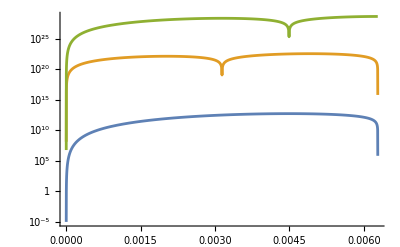

```mathematica
T=2π/Ω//.params;
Plot[Abs[vListP]//Evaluate,{t,0,1T},ScalingFunctions->"Log"]
```

### Coupling term

```mathematica
$Assumptions={ℏ>0,ω>0,m>0,Ω>0,G0>0,ϵ>0,ωG>0,G>0,G0>0,ϵ>0,ωG>0};
hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0}/.{G->G0(1+θ Cos[ωG t])};
Transpose@{hCoeffs,algebra}
```

{{0,1},{ω ℏ,n̂},{0,n̂∘n̂},{g m,x̂},{0,p̂},{(m Ω^2)/2,x̂∘x̂},{1/(2 m),p̂∘p̂},{0,x̂∘p̂},{-G0 ℏ (1+θ Cos[t ωG]),n̂∘x̂},{0,n̂∘p̂}}

```mathematica
θVal=0;
dhj=D[hCoeffs,θ]
hj=hCoeffs
```

{0,0,0,0,0,0,0,0,-G0 ℏ Cos[t ωG],0}

{0,ω ℏ,0,g m,0,(m Ω^2)/2,1/(2 m),0,-G0 ℏ (1+θ Cos[t ωG]),0}

```mathematica
dvList=Table[(dhj[[j]]+ⅈ Sum[AlgStructureΓ[k,l,j,algebra]v[k,t]hj[[l]],{k,1,Length@algebra},{l,1,Length@algebra}])/ℏ,{j,1,Length@algebra}]//FullSimplify;
vEqs=Table[D[v[j,t],t]==dvList[[j]],{j,1,Length@algebra}];
Print/@vEqs;
```

v^(0,1)[1,t]==g m v[5,t]+(ⅈ ℏ (v[6,t]-m^2 Ω^2 v[7,t]))/m

v^(0,1)[2,t]==-G0 ℏ (1+θ Cos[t ωG]) v[5,t]+g m v[10,t]

v^(0,1)[3,t]==-G0 ℏ (1+θ Cos[t ωG]) v[10,t]

v^(0,1)[4,t]==m (Ω^2 v[5,t]+g v[8,t])

v^(0,1)[5,t]==-v[4,t]/m+2 g m v[7,t]

v^(0,1)[6,t]==m Ω^2 v[8,t]

v^(0,1)[7,t]==-v[8,t]/m

v^(0,1)[8,t]==-(2 v[6,t])/m+2 m Ω^2 v[7,t]

v^(0,1)[9,t]==-G0 Cos[t ωG]-G0 ℏ (1+θ Cos[t ωG]) v[8,t]+m Ω^2 v[10,t]

v^(0,1)[10,t]==-2 G0 ℏ (1+θ Cos[t ωG]) v[7,t]-v[9,t]/m

```mathematica
ExpandByHAlg[algebra,n̂∘x̂,2]
algebra[[{2,3,9,10}]]
```

{n̂∘x̂,n̂,n̂∘p̂,n̂∘n̂}

{n̂,n̂∘n̂,n̂∘x̂,n̂∘p̂}

```mathematica
eqsRed={vEqs[[2]],vEqs[[3]],vEqs[[9]],vEqs[[10]]}/.{v[1,t]->0,v[4,t]->0,v[5,t]->0,v[6,t]->0,v[7,t]->0,v[8,t]->0}
```

{v^(0,1)[2,t]==g m v[10,t],v^(0,1)[3,t]==-G0 ℏ (1+θ Cos[t ωG]) v[10,t],v^(0,1)[9,t]==-G0 Cos[t ωG]+m Ω^2 v[10,t],v^(0,1)[10,t]==-v[9,t]/m}

```mathematica
vSol=Flatten@DSolve[Join[eqsRed,{v[2,0]==0,v[3,0]==0,v[9,0]==0,v[10,0]==0}],{v[2,t],v[3,t],v[9,t],v[10,t]},t]//FullSimplify;
```

```mathematica
Print/@vSol;
```

v[2,t]→(-g G0 ωG Sin[t Ω]+g G0 Ω Sin[t ωG])/(Ω^3 ωG-Ω ωG^3)

v[3,t]→(G0^2 ℏ (4 ωG (Ω^2-ωG^2+θ Ω^2 Cos[t ωG]) Sin[t Ω]-4 θ Ω ωG^2 Cos[t Ω] Sin[t ωG]+Ω (-Ω+ωG) (Ω+ωG) (4 Sin[t ωG]+θ (2 t ωG+Sin[2 t ωG]))))/(4 m Ω ωG (Ω^2-ωG^2)^2)

v[9,t]→(-G0 Ω Sin[t Ω]+G0 ωG Sin[t ωG])/(Ω^2-ωG^2)

v[10,t]→(G0 (-Cos[t Ω]+Cos[t ωG]))/(m (Ω^2-ωG^2))

```mathematica
v3exp=(G0^2 ℏ (-2 (Ω-ωG) (Ω+ωG) (-2 ωG^2+Ω^2 (2+t θ ωG))-4 ωG^2 Cos[t Ω] (Ω^2-ωG^2+θ Ω^2 Sin[t ωG])+2 Ω Cos[t ωG] (2 θ ωG^3 Sin[t Ω]+Ω (Ω-ωG) (Ω+ωG) (2+θ Sin[t ωG]))))/(4 m ωG (Ω^3-Ω ωG^2)^2);
```

```mathematica
a=(v[3,t]/.vSol)
```

(G0^2 ℏ (4 ωG (Ω^2-ωG^2+θ Ω^2 Cos[t ωG]) Sin[t Ω]-4 θ Ω ωG^2 Cos[t Ω] Sin[t ωG]+Ω (-Ω+ωG) (Ω+ωG) (4 Sin[t ωG]+θ (2 t ωG+Sin[2 t ωG]))))/(4 m Ω ωG (Ω^2-ωG^2)^2)

```mathematica
b=(ℏ G0^2)/(4 m Ω ωG (Ω^2-ωG^2)^2) ((Ω^2-ωG^2)*(4( ωG Sin[t Ω]- Ω Sin[t ωG])-θ Ω(2 t ωG+Sin[2 t ωG]) )+4 θ ωG  Ω (Ω Cos[t ωG] Sin[t Ω]- ωG Cos[t Ω] Sin[t ωG]));
b-a//FullSimplify
```

0

```mathematica
vResonance=Limit[Last/@vSol,{ωG->Ω}]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{(g G0 (-t Ω Cos[t Ω]+Sin[t Ω]))/(2 Ω^3),(G0^2 ℏ (4 t Ω Cos[t Ω]+t θ Ω Cos[2 t Ω]-(4+θ Cos[t Ω]) Sin[t Ω]))/(8 m Ω^3),-(G0 (t Ω Cos[t Ω]+Sin[t Ω]))/(2 Ω),(G0 t Sin[t Ω])/(2 m Ω)}

```mathematica
Print/@vResonance;
```

(g G0 (-t Ω Cos[t Ω]+Sin[t Ω]))/(2 Ω^3)

(G0^2 ℏ (4 t Ω Cos[t Ω]+t θ Ω Cos[2 t Ω]-(4+θ Cos[t Ω]) Sin[t Ω]))/(8 m Ω^3)

-(G0 (t Ω Cos[t Ω]+Sin[t Ω]))/(2 Ω)

(G0 t Sin[t Ω])/(2 m Ω)

### Squeezing

```mathematica
$Assumptions={ℏ>0,ω>0,m>0,Ω>0,G0>0,ϵ>0,ωg>0,G>0,G0>0,ϵ>0,ωG>0,Ω0>0,ωm>0,θ>0,t>0};
hCoeffs={0,ℏ ω,0,m g,0,1/2 m Ω^2,1/(2m),0,-ℏ G,0}/.{Ω^2->Ω0^2+θ Cos[Ωm t]};
Transpose@{hCoeffs,algebra}
```

{{0,1},{ω ℏ,n̂},{0,n̂∘n̂},{g m,x̂},{0,p̂},{1/2 m (Ω0^2+θ Cos[t Ωm]),x̂∘x̂},{1/(2 m),p̂∘p̂},{0,x̂∘p̂},{-G ℏ,n̂∘x̂},{0,n̂∘p̂}}

```mathematica
θVal=0;
dhj=D[hCoeffs,θ]
hj=hCoeffs
```

{0,0,0,0,0,1/2 m Cos[t Ωm],0,0,0,0}

{0,ω ℏ,0,g m,0,1/2 m (Ω0^2+θ Cos[t Ωm]),1/(2 m),0,-G ℏ,0}

```mathematica
dvList=Table[(dhj[[j]]+ⅈ Sum[AlgStructureΓ[k,l,j,algebra]v[k,t]hj[[l]],{k,1,Length@algebra},{l,1,Length@algebra}])/ℏ,{j,1,Length@algebra}]//FullSimplify;
vEqs=Table[D[v[j,t],t]==dvList[[j]],{j,1,Length@algebra}];
Print/@vEqs;
```

v^(0,1)[1,t]==g m v[5,t]+(ⅈ ℏ (v[6,t]-m^2 (Ω0^2+θ Cos[t Ωm]) v[7,t]))/m

v^(0,1)[2,t]==-G ℏ v[5,t]+g m v[10,t]

v^(0,1)[3,t]==-G ℏ v[10,t]

v^(0,1)[4,t]==m ((Ω0^2+θ Cos[t Ωm]) v[5,t]+g v[8,t])

v^(0,1)[5,t]==-v[4,t]/m+2 g m v[7,t]

v^(0,1)[6,t]==(m Cos[t Ωm])/(2 ℏ)+m (Ω0^2+θ Cos[t Ωm]) v[8,t]

v^(0,1)[7,t]==-v[8,t]/m

v^(0,1)[8,t]==-(2 v[6,t])/m+2 m (Ω0^2+θ Cos[t Ωm]) v[7,t]

v^(0,1)[9,t]==-G ℏ v[8,t]+m (Ω0^2+θ Cos[t Ωm]) v[10,t]

v^(0,1)[10,t]==-(2 G m ℏ v[7,t]+v[9,t])/m

```mathematica
vEqsθ0=vEqs/.θ->0;
v678Sol0=Flatten@DSolveValue[Join[vEqsθ0[[6;;8]],{v[6,0]==0,v[7,0]==0,v[8,0]==0}],{v[6,t],v[7,t],v[8,t]},t]//FullSimplify;
v6=v678Sol0[[1]]
v7=v678Sol0[[2]]
v8=v678Sol0[[3]]
```

(m (Ω0 Ωm Sin[2 t Ω0]+(2 Ω0^2-Ωm^2) Sin[t Ωm]))/(8 Ω0^2 Ωm ℏ-2 Ωm^3 ℏ)

(-Ωm Sin[2 t Ω0]+2 Ω0 Sin[t Ωm])/(8 m Ω0^3 Ωm ℏ-2 m Ω0 Ωm^3 ℏ)

(Cos[2 t Ω0]-Cos[t Ωm])/(4 Ω0^2 ℏ-Ωm^2 ℏ)